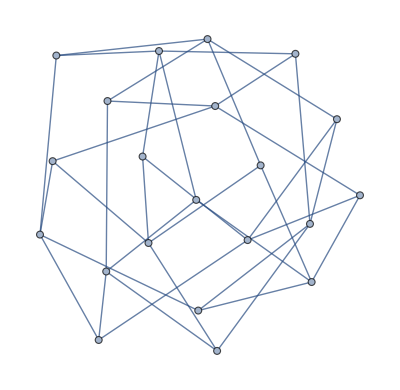

```mathematica
g=Graph[{1<->A,1<->B,1<->C,1<->D,2<->A,2<->E,2<->F,2<->G,3<->A,3<->H,3<->L,3<->M,4<->B,4<->E,4<->H,4<->I,5<->B,5<->F,5<->L,5<->N,6<->C,6<->E,6<->M,6<->N,7<->C,7<->G,7<->I,7<->L,8<->D,8<->F,8<->I,8<->M,9<->D,9<->G,9<->H,9<->N}]
```

```mathematica
FindHamiltonianCycle[g]
```

{}

```mathematica
(*
	Questa funzione disegna un grafo derivato dal piano di Fano.

INPUT: prm permutazione dei 14 nodi (default la permutazione identica) (un nodo puo' permutare con un nodo dello stesso colore)
	   cx  coordinata X del centro del grafo (default 0)
	   nfs rotazione del grafo. Viene realizzata una rotazione in senso antiorario di angolo nsf*(180/7 gradi)
		   Se nfs e' intero questo corrisponde ad una rotazione dei nodi.
OUTPUT: Elemento da graficare
     
*)
genFano[prm_:{0},cx_:0,nfs_:0]:=(
clr1=Black;
clr2=Green;
cy=0;
r=10;
dfs=Pi/2+Pi/14;
da=2Pi/14;
If[prm[[1]]==0,perm=Range[14],perm=prm];

lcoo=Range[14];
lcoot1=Range[14];
lcoot2=Range[14];
lcoot3=Range[14];
ang=0;
offs1=2;
offs2=4;
offs3=6;
fs=Pi/7 nfs;
For[k=1,k≤14,k++,
pp={cx+r Cos[ang+dfs+fs],cy+r Sin[ang+dfs+fs]};
lcoo[[perm[[k]]]]=pp;
lcoot1[[perm[[k]]]]={pp[[1]]+offs1 Cos[ang+dfs+fs],pp[[2]]+offs1 Sin[ang+dfs+fs] };
lcoot2[[perm[[k]]]]={pp[[1]]+offs2 Cos[ang+dfs+fs],pp[[2]]+offs2 Sin[ang+dfs+fs] };
lcoot3[[perm[[k]]]]={pp[[1]]+offs3 Cos[ang+dfs+fs],pp[[2]]+offs3 Sin[ang+dfs+fs] };
ang-=da
];

lpagg1=List[10,7,12,9,14,11,2,13,4,1,6,3,8,5];
colors={"Red","Blue"};
p=Range[14];
sizep=10;
For[k=1,k≤14,k+=2,
p[[k]]={AbsolutePointSize[sizep],RGBColor[colors[[Mod[k-1,2]+1]]],Point[lcoo[[k]]],Text[Floor[k/2]+1,lcoot1[[k]]]}
];
For[k=2,k≤14,k+=2,
p[[k]]={AbsolutePointSize[sizep],RGBColor[colors[[Mod[k-1,2]+1]]],Point[lcoo[[k]]],Text[Mod[Floor[(k-2)/2],15]+1,lcoot1[[k]]],Text[Mod[Floor[k/2],15]+1,lcoot2[[k]]],Text[Floor[lpagg1[[k]]/2+1],lcoot3[[k]]]}
];

ln=Range[14];
For[k=1,k≤13,k++,
ln[[k]]=Line[{lcoo[[k]],lcoo[[k+1]]}]
];
ln[[14]]=Line[{lcoo[[14]],lcoo[[1]]}];

lpagg=List[{1,10},{2,7},{3,12},{4,9},{5,14},{6,11},{8,13}];
lnaus=Range[7];
For[k=1,k≤7,k++,
lnaus[[k]]=Line[{lcoo[[lpagg[[k]][[1]]]],lcoo[[lpagg[[k]][[2]]]]}]
];

Return[{p,{clr1,ln},{clr2,lnaus}}];
)
```

```mathematica
(*
	Questa funzione applica una serie di trasposizioni ad una permutazione di partenza

	INPUT: per insieme delle trasposizioni da applicare
		 n   numero di elementi della permutazione di partenza
		 prm permutazione di partenza (default la permutazione identica su n elementi)
*)
genPerm[per_,n_,prm_:{0}]:=(
If[prm[[1]]==0,result=Range[n],result=prm];
nel1=Length[per];
For[k1=1,k1≤nel1,k1++,
nel2=Length[per[[k1]]];
For[k2=nel2,k2>=1,k2--,
inda=per[[k1]][[k2]];
If[k2<nel2,result[[indp]]=result[[inda]],appo=result[[inda]]];
indp=inda;
];
result[[indp]]=appo;
];
Return[result];
)

(*
	Questa funzione applica una riflessione ad una permutazione iniziale di vertici
   La riflessione e' effettuata rispetto ad un asse che passa per il vertice v1
   se v1=v2 o passa per la mediana del lato che congiunge v1 a v2 (dovra' essere v2=(v1+1 modulo n) 

	INPUT: v1  primo vertice
		 v2  secondo vertice
		 n   numero dei vertici
		 prm permutazione iniziale di n vertici
*)
genRiflex[v1_,v2_,n_,prm_:{0}]:=(
If[prm[[1]]==0,result=Range[n],result=prm];
If[v1==v2,
v=v1;
For[k=1,k≤Floor[(n-1)/2],k++,
appo=result[[Mod[v-1-k,n]+1]];
result[[Mod[v-1-k,n]+1]]=result[[Mod[v-1+k,n]+1]];
result[[Mod[v-1+k,n]+1]]=appo
],
For[k=1,k≤Floor[n/2],k++,
appo=result[[Mod[v1-k,n]+1]];
result[[Mod[v1-k,n]+1]]=result[[Mod[v2+k-2,n]+1]];
result[[Mod[v2+k-2,n]+1]]=appo
]
];
Return[result];
)
```

```mathematica
Graphics[genFano[]]
```

```mathematica
gen1={{5,9},{6,8},{10,14},{11,13}};
gen2={{4,12},{5,11},{9,13},{10,14}};
gen3={{2,14},{3,5},{6,12},{7,13}};
gen4={{1,3},{4,14},{9,13},{10,12}};

g1=genFano[genPerm[gen1,14]];
g2=genFano[genPerm[gen2,14],40];
g3=genFano[genPerm[gen3,14],80];
g4=genFano[genPerm[gen4,14],120];
Graphics[{g1,g2,g3,g4}]
```